96

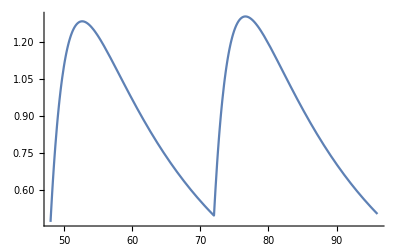

```mathematica
SetDirectory[NotebookDirectory[]];

(*Import of demographic factors*)

demographics=Import["demo-par.txt","Table"];
(*SWITCH for data analysis*)
sw=Flatten[demographics][[4]];

bw=Flatten[demographics][[1]];
age=Flatten[demographics][[2]];
sex=Flatten[demographics][[3]];
(*Evaluation of PK parameters from Widmer et al.*)
mage=50;
mbw=70;

tetaa=12.8;
tetab=258;
teta1=12.7;
teta2=0.8;
teta3=-2.1;
teta4=-1;
teta5=61;
(*evaluation of personal parameters*)

cl=tetaa+teta1*(bw-mbw)/mbw+teta2*sex-(1-sex)*teta2+teta3*(age-mage)/mage+teta4;
ka=0.437;
v=tetab+teta5*sex-(1-sex)*teta5;


(*EVALUATION OF PERSONAL PD*)

(*If data analysis is not required export of results*)
If[sw==0,{
result=Table[0,{3}],
result[[1]]=cl,
result[[2]]=v,
result[[3]]=ka,Export["personal.dat",result]

}]



(*If data analysis is required*)








If[sw==1,{
result=Table[0,{4}],
result[[1]]=cl,
result[[2]]=v,
result[[3]]=ka,
(*Linear analysis*)
dati=Import["Data-TB.xls","Data"],
(*Cleaning data file of excel*)time=DeleteCases[ToExpression[dati[[1]][[1]]],Null],
value=DeleteCases[ToExpression[dati[[1]][[2]]],Null],
s=Length[time],
vettpaz=Table[0,{s}],
For[k=1,k≤s,k++,{
vettpaz[[k]]={30*time[[k]],Log10[value[[k]]]}}],
(*Inizialization of value for analysis*)
test2=0,
testbest=0,
abest=0,
bbest=0,
cbest=0,
dbest=0,
tbest=0,
ClearAll[a,b,c,d],
For[f=vettpaz[[1]][[1]],f≤vettpaz[[s]][[1]],f++,{
fit2=NonlinearModelFit[vettpaz,Piecewise[{{a*t+b,t<f},{c*t+a*f+b-c*f,t≥f}}],{a,b,c,d},t],
myA=a/.fit2["BestFitParameters"],
myB=b/.fit2["BestFitParameters"],
myC=c/.fit2["BestFitParameters"],
myD=d/.fit2["BestFitParameters"],
test2=fit2["RSquared"],If[test2≥testbest,{testbest=test2,abest=myA,bbest=myB,cbest=myC,dbest=myD,tbest=f}]}],
(*evaluation of personal PD*)
ndose=4,
kk=1/0.377,
f=1,
tmax=ndose*(24/Flatten[demographics][[6]]),
p1=0.45,
     a1=0.87,
vdosi=Table[Flatten[demographics][[5]],{ndose}],
xgv=Table[0,{ndose}],
xgv[[1]]=f*vdosi[[1]]*Exp[-ka*t],
For[i=2,i≤ndose,i++,{xgv[[i]]=xgv[[i-1]]+UnitStep[t-(24/Flatten[demographics][[6]])*(i-1)]*f*vdosi[[i]]*Exp[-ka*(t-(i-1)*(24/Flatten[demographics][[6]]))]}],
ClearAll[t],eqsc=Join[{D[cp[t],t]==-cl*cp[t]/v+ka*xgv[[ndose]],cp[0]==0}],
solc=NDSolve[eqsc,cp[t],{t,0,tmax}],avg=Simplify[(NIntegrate[Evaluate[cp[t]/.solc]/v,{t,48,tmax}][[1]])/(tmax-48)],
di=((2*a1-1)*p1-(cbest)/Log10[N[E]]),n2=(avg-(kk)*di*avg)/((kk)*di),

result[[4]]=n2,
Export["personal.dat",result]
}]
```

```mathematica
ka
```

0.437